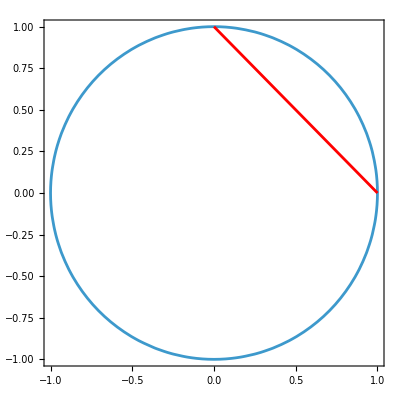

```mathematica
Show[
  ContourPlot[
    x^2+y^2==1,
    {x,-1,1},
    {y,-1,1},
    PlotRange->{{-1,1},{-1,1}}
  ],
  ParametricPlot[
    {
      Re[(1-α)+I α],
      Im[(1-α)+I α]
    },
    {α,0,1},
    PlotRange->{{-1,1},{-1,1}},
    AxesLabel->{"Re","Im"},
    PlotStyle->Red
  ]
]
```

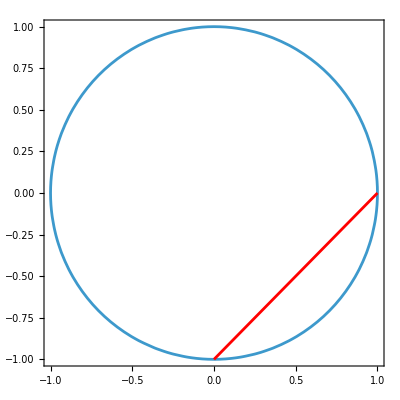

```mathematica
Show[
  ContourPlot[
    x^2+y^2==1,
    {x,-1,1},
    {y,-1,1},
    PlotRange->{{-1,1},{-1,1}}
  ],
  ParametricPlot[
    {
      Re[(1-α)-I α],
      Im[(1-α)-I α]
    },
    {α,0,1},
    PlotRange->{{-1,1},{-1,1}},
    AxesLabel->{"Re","Im"},
    PlotStyle->Red
  ]
]
```